```mathematica
(*run with CVnoisyStorageRates !! *)
```

```mathematica
(* Parameters *) 

n = 2*10^5;  (* number of signals*) 
ϵA0=10^-7;   (* security epsilon *) 
δ = 0.1; (*the bin size in the discretization of the data*)
alphabet=2^10; (* the size of the alphabet for discretization *)
α=δ * alphabet/2;(*the cut-off parameter *)
(* Parameter for the attackers memory *)
Nmax0=100; (*number of maximal photon numbers *)
eta0=0.75; (* transmission of QM*) 
betasimulation = 0.925; (* error correction efficiency *)

(* two graphs for different number of QM fractions *) 
ν0=0.001;
ν1=0.01;
```

```mathematica
eta=1-5.8/100; (* optical efficiency *)
TplusL = 0.1018; (* T: transmissivity of coupling mirror, L intra cavity loss *)
l= 79.8*10^-3; (* cavity length *)
```

```mathematica
Clear[sq]
sqz[x_] := 1-eta*4*x/((1+x)^2+4*((2*Pi*8*10^6)/TplusL/3/10^8*l)^2);
anti[x_] := 1+eta*4*x/((1-x)^2+4*((2*Pi*8*10^6)/TplusL/3/10^8*l)^2);
f = Solve[sqz[x] == sq, x];
g[y_]:=x/.f[[2]]/.sq->y;
antisqz[linsqz_] := anti[g[linsqz]];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

LogPlot::exclul: {Im[-1.29894×10^11\ 10.^-0.2\ x + 7.35284×10^12\ 10.^-0.1\ x] - 0, Im[-1.29894×10^11\ 10.^-0.2\ x + 7.35284×10^12\ 10.^-0.1\ x] - 0, 1.66804×10^-10\ Im[-1.9969×10^10 - 2.25893×10^10\ Power[« 2 »] + 16464.3\ Power[« 2 »]/(-1. + Power[« 2 »])\ (0.0690029  + Power[« 2 »])] - 0, « 46 », 0.94\ Im[10.^0.05\ Plus[« 2 »]\ Cosh[0.230259\ Plus[« 2 »]]] - 0, « 26 »} must be a list of equalities or real-valued functions.

LogPlot::exclul: {Im[-1.29894×10^11\ 10.^-0.2\ x + 7.35284×10^12\ 10.^-0.1\ x] - 0, Im[-1.29894×10^11\ 10.^-0.2\ x + 7.35284×10^12\ 10.^-0.1\ x] - 0, 1.66804×10^-10\ Im[-1.9969×10^10 - 2.25893×10^10\ Power[« 2 »] + 16464.3\ Power[« 2 »]/(-1. + Power[« 2 »])\ (0.0690029  + Power[« 2 »])] - 0, « 46 », 0.665\ Im[10.^0.05\ Plus[« 2 »]\ Cosh[0.230259\ Plus[« 2 »]]] - 0, « 26 »} must be a list of equalities or real-valued functions.

LogPlot::exclul: {Im[-1.29894×10^11\ 10.^-0.2\ x + 7.35284×10^12\ 10.^-0.1\ x] - 0, Im[-1.29894×10^11\ 10.^-0.2\ x + 7.35284×10^12\ 10.^-0.1\ x] - 0, 1.66804×10^-10\ Im[-1.9969×10^10 - 2.25893×10^10\ Power[« 2 »] + 16464.3\ Power[« 2 »]/(-1. + Power[« 2 »])\ (0.0690029  + Power[« 2 »])] - 0, « 46 », 0.82\ Im[10.^0.05\ Plus[« 2 »]\ Cosh[0.230259\ Plus[« 2 »]]] - 0, « 26 »} must be a list of equalities or real-valued functions.

General::stop: Further output of LogPlot :: exclul will be suppressed during this calculation.

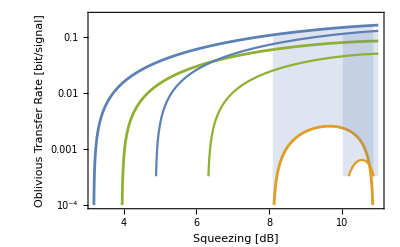

```mathematica
points = 2000;
PlotExp=Show[LogPlot[{
rateOTgauss[δ,GAB[x,10*Log10[antisqz[10^(-x/10)]],0.03, 0.03+0.03,0,0],betasimulation,2*10^5,ϵA0,α0,ν0,Nmax0,eta0],
rateOTgauss[δ,GAB[x,10*Log10[antisqz[10^(-x/10)]],0.03, 0.03+0.305,0,0],betasimulation,2*10^5,ϵA0,α0,ν0,Nmax0,eta0],
rateOTgauss[δ,GAB[x,10*Log10[antisqz[10^(-x/10)]],0.03, 0.03+0.15,0,0],betasimulation,2*10^5,ϵA0,α0,ν0,Nmax0,eta0]},{x,2,11},Filling->{1->{2}},PlotPoints->points,PlotRange->{10^-4,Automatic},PlotStyle-> Thickness[0.005],LabelStyle->Directive[Black,FontSize->12],FrameStyle->Thickness[0.0035],Frame->{{True,True},{True,True}},FrameLabel->{"Squeezing [dB]","Oblivious Transfer Rate [bit/signal]"},
BaseStyle->{FontFamily->"Times New Roman",FontSize->16}],
LogPlot[{
rateOTgauss[δ,GAB[x,10*Log10[antisqz[10^(-x/10)]],0.03, 0.03+0.03,0,0],betasimulation,2*10^5,ϵA0,α0,ν1,Nmax0,eta0],
rateOTgauss[δ,GAB[x,10*Log10[antisqz[10^(-x/10)]],0.03, 0.03+0.239,0,0],betasimulation,2*10^5,ϵA0,α0,ν1,Nmax0,eta0],
rateOTgauss[δ,GAB[x,10*Log10[antisqz[10^(-x/10)]],0.03, 0.03+0.15,0,0],betasimulation,2*10^5,ϵA0,α0,ν1,Nmax0,eta0]},{x,2,11},Filling->{1->{2},PlotPoints->points}]]
```

```mathematica
Export["OTSqueezingPlot.pdf",PlotExp]
```

OTSqueezingPlot.pdf